ToDo:  
Figure out how to choose beta.  One idea is that we balance the contribution of the non-beta term with the beta term so that each contributes equally to the reward function (easy to do).  A more convincing method would be to find a point where the policy is halfway between the beta=0 and beta=large policies (not so easy).

Try to add new features and remove features.  This must be done after we settle on value for beta.  Use correlation matrix for states to determine best candidates for removal.

Eventually (after first iteration), need to figure out when random-help policy should be applied.  If we only choose optimal help based on current best guess, we may not explore parts of policy-space vs. state that need exploring.  As we increase the amount of data, the fraction of time we use the random policy should decrease.  We need some estimate of the probability that the second-best policy is, in fact, the best policy.

On logistic vs. step:  The distance of a point in feature space to the hyperplane has no meaning since we have not formulated a metric in that space.  Using a logistic function of the distance between point and the hyperplane (function linearPolicy) thus doesn't make much sense.  The Budinich paper uses the logistic but only as a numerical trick.  In our numerical experiments, the global fit routines performed much better than the gradient-based routines anyway so the main motivation for this numerical trick doesn't apply.  [Note that the whole discussion of choosing beta in the Budinich paper is nonsense anyway since it is equivalent to rescaling the equation for the hyperplane.]

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Volumes/BRETT-STUFF

### State

```mathematica
Dimensions[state=Import["state-uwplatt.csv"]]
```

{15327,10}

```mathematica
state[[1]]
```

{ttID,logSessionTime,fracSessionFlounderTime,logNowFlounderSteps,logNowFlounderTime,logNowStepTime,sessionCorrect,sessionIncorrect,sessionHelp,fracSessionCorrect}

Create hash table for fast lookup

```mathematica
Map[(state1[#[[1]]]=Rest[#])&,Rest[state]];
nFeatures=Length[Rest[state[[1]]]]
```

9

### Reward

```mathematica
Dimensions[reward=Import["reward-0.5-md5:e2ed3385.csv"]]
```

{59,10}

```mathematica
Dimensions[reward=Import["reward-0.5-uwplatt-2Y130.csv"]]
```

{812,12}

```mathematica
Dimensions[reward=Import["reward-0.5-uwplatt.csv"]]
```

{7210,12}

This must be reset any time a reward file is loaded :

```mathematica
Clear[rewardPosition];rewardPosition[x_]:=rewardPosition[x]=First[First[Position[reward[[1]],x,1,1]]];
rewardValue[x_,y_]:=x[[rewardPosition[y]]]
```

```mathematica
reward[[1]]
```

{KC,clientID,ttID,learning,oppTurns,noSlip,spontaneous-hint,no-hints,GIVE-BACKWARDS-HINTS,zz-unclassified-hint,forwards-hint,zz-extra-hint}

### Evaluate State & Reward

```mathematica
Map[Histogram[Rest[#],PlotLabel->First[#],PlotRange->All]&,Transpose[Map[Rest,state]]]
```

```mathematica
TableForm[Correlation[Map[Rest,Rest[state]]],TableHeadings->{Rest[state[[1]]],Rest[state[[1]]]}]
```

| logSessionTime | fracSessionFlounderTime | logNowFlounderSteps | logNowFlounderTime | logNowStepTime | sessionCorrect | sessionIncorrect | sessionHelp | fracSessionCorrect
logSessionTime | 1. | 0.651338 | 0.311562 | 0.301274 | 0.0736642 | 0.721848 | 0.642297 | 0.501846 | -0.417251
fracSessionFlounderTime | 0.651338 | 1. | -0.0575093 | -0.0696664 | -0.0705747 | 0.428488 | 0.477 | 0.32602 | -0.370403
logNowFlounderSteps | 0.311562 | -0.0575093 | 1. | 0.962906 | 0.0545284 | 0.0111198 | 0.26894 | 0.192042 | -0.476544
logNowFlounderTime | 0.301274 | -0.0696664 | 0.962906 | 1. | 0.109902 | 0.00164358 | 0.22699 | 0.139857 | -0.45948
logNowStepTime | 0.0736642 | -0.0705747 | 0.0545284 | 0.109902 | 1. | -0.0444632 | -0.0232201 | -0.150746 | -0.0172625
sessionCorrect | 0.721848 | 0.428488 | 0.0111198 | 0.00164358 | -0.0444632 | 1. | 0.661039 | 0.489532 | -0.0344468
sessionIncorrect | 0.642297 | 0.477 | 0.26894 | 0.22699 | -0.0232201 | 0.661039 | 1. | 0.397376 | -0.319528
sessionHelp | 0.501846 | 0.32602 | 0.192042 | 0.139857 | -0.150746 | 0.489532 | 0.397376 | 1. | -0.26693
fracSessionCorrect | -0.417251 | -0.370403 | -0.476544 | -0.45948 | -0.0172625 | -0.0344468 | -0.319528 | -0.26693 | 1.

List different policy combinations and number of instances of each

```mathematica
Block[{pp=Map[Drop[#,6]&,Rest[reward]]},Map[{#,Count[pp,#]}&,Union[pp]]]
```

{{{0,0,1,0},2},{{0,1,0,0},17},{{0,1,0,1},2},{{1,0,0,0},37}}

### Analyze routines

Policy choice is represented by a 0 or 1; -1 means policy doesn' t apply.  There is some nonsense in Budinich paper about -1 & 1 being preferred, but Eqn. (2) in paper is effectively the same for either convention.

```mathematica
policyVector[x_]:={Which[rewardValue[x,"no-hints"]==1,0,rewardValue[x,"spontaneous-hint"]==1,1,True,-1],
Which[rewardValue[x,"GIVE-BACKWARDS-HINTS"]==1,1,rewardValue[x,"forwards-hint"]==1,0,True,-1]};
policyVector[x_,y_]:=policyVector[x][[y]];
nPolicies=2;  (* Number of policies *)
comparePolicies[x_,y_]:=If[x===-1||y===-1,0,(x-y)^2] (* For policy to not apply, -1 must be explicit *);
invertPolicy[x_]:=If[x<0,x,1-x]
```

```mathematica
useStep=True; (* Choose between step function and a logistic *)
linearPolicy[state_,x_]:=Block[{a=Drop[x,-1],b=x[[-1]]},Block[{h=a.state+b  (* divide this by Sqrt[a.a] to get distance of state from hyperplane. *)},If[ useStep,(Sign[h]+1)/2,(Tanh[h/(2 Sqrt[a.a])]+1)/2]]]
```

Maybe should have weight for integrated probability (probability student has already learned skill before this step).

```mathematica
rewardFunctionTerm[beta_,x_,policy_,r_]:= 
Block[{pp=linearPolicy[state1[r[[3]]],x]},If[r[[4]]>0 ,(r[[5]]+beta r[[6]])/r[[4]] comparePolicies[pp,policyVector[r,policy]],0]];
rewardFunction[beta_,x_]:=Sum[rewardFunction[beta,x[[i]],i],{i,nPolicies}];rewardFunction[beta_,x_,policy_]:=Apply[Plus,Map[rewardFunctionTerm[beta,x,policy,#]&,Rest[reward]]]
```

```mathematica
globalMinimum=True; (* Find global minimum or use gradient method for local *)
minimizer[fcn_,xx_,opts___]:=If[globalMinimum,NMinimize[fcn,xx,opts],FindMinimum[fcn,Map[{#,(Random[]-0.5)}&,xx],opts]];
minit[beta_,policy_,opts___]:=Block[{xx=Table[x[i],{i,nFeatures+If[useStep,0,1]}],zz,zzz,yy,yyy},
If[useStep,
(* Try each side of hyperplane and take best fit.  Use b=-1 or +1 as normalization. *)
yy=Append[xx,1];
zz=minimizer[rewardFunction[beta,yy,policy],xx,opts];
yyy=Append[xx,-1];
zzz=minimizer[rewardFunction[beta,yyy,policy],xx,opts];
	If[First[zzz]<First[zz],zz=zzz;yy=yyy],
(* For logistic, b is a fit parameter. *) 
yy=xx;zz=minimizer[rewardFunction[beta,yy,policy],xx,opts]];{First[zz],yy/.zz[[2]]}];
(* Add up the contribution from each policy to the reward function *)
minP[beta_,opts___]:=Block[{mp=Table[minit[beta,i,opts],{i,nPolicies}]},{Apply[Plus,Map[First,mp]],Map[#[[2]]&,mp]}]
```

Count, for each step where a policy choice can be made, number of instances of each policy choice or pair of policy choices.  If input is not a list, use original choice taken by Andes.

```mathematica
getPolicyVector[x_,r_]:=If[Head[x]===List,Map[linearPolicy[state1[r[[3]]],#]&,If[MatrixQ[x],x,Partition[x,nFeatures+1]]],policyVector[r]];
dist[x_]:=Block[{y=Map[getPolicyVector[x,#]&,Rest[reward]]},TableForm[Map[Count[y,#]&,Union[y]],TableHeadings->{Union[y],None}]];
dist[x_,y_]:=Block[{z=Map[{getPolicyVector[x,#],getPolicyVector[y,#]}&,Rest[reward]],hx,hy},hx=Union[Map[#[[1]]&,z]];hy=Union[Map[#[[2]]&,z]];TableForm[Outer[Count[z,{#1,#2}]&,hx,hy,1],TableHeadings->{hx,hy}]]
```

### Analyze

Calculate random data point

```mathematica
rewardFunction[1.0,Table[(Random[]-0.5)*10,{nPolicies},{nFeatures+1}]]
```

6.3187

```mathematica
Block[{useStep=False},rewardFunction[1.0,Table[(Random[]-0.5)*10,{nPolicies},{nFeatures+1}]]]
```

7.28952

```mathematica
Timing[Block[{useStep=False},soln1=minP[1.0]]]
```

{3.58646,{2.78029,{{-5904.86,6270.59,-117.745,5899.46,7714.42,1198.29,968.392,-8142.48,16082.6,-64748.9},{-0.0178304,-0.0277821,0.100176,0.121774,0.0442524,-0.0567074,-0.512038,-0.114251,0.000229068,33.4411}}}}

```mathematica
Timing[soln1=minP[1.0]]
```

{0.550916,{4.71059,{{-0.800686,0.631044,0.860357,0.235238,0.90166,0.233556,0.00420671,-0.293701,-0.349429,-1},{-0.818516,0.632805,0.913456,0.2798,0.91426,0.270753,-0.0181918,-0.259239,-0.371446,-1}}}}

```mathematica
dist[0]
```

{-1,1} | 2
{0,-1} | 37
{1,-1} | 17
{1,0} | 2

```mathematica
dist[soln1[[2]]]
```

{0,0} | 15
{1,0} | 3
{1,1} | 40

### Different values of beta (step)

#### Calculate solutions

```mathematica
Timing[soln[0]=minP[0,Method->"DifferentialEvolution"]]
```

{14.3818,{1.51847,{{-7.1366,-3.87468,-2.28018,-2.16215,0.325936,6.02643,-2.46843,6.107,-2.00169,-1},{-4.47441,-10.7517,-8.33127,-3.13662,-19.1568,-10.7888,-4.965,4.47602,-4.5182,1}}}}

```mathematica
Timing[soln[1/16]=minP[1/16,Method->"DifferentialEvolution"]]
```

{28.9556,{3.80224,{{-3.99841,1.54608,2.10108,-2.22334,0.916731,2.47209,-0.963671,2.49746,6.45649,-1},{1.19978,1.76344,-0.123296,2.33285,-1.70962,-1.6799,-2.57694,1.443,1.01734,1}}}}

```mathematica
Timing[soln[1/8]=minP[0.125,Method->"DifferentialEvolution"]]
```

{26.157,{5.9425,{{-2.23696,1.34972,-2.38337,0.297161,1.63183,0.529343,-0.444648,1.8025,-6.71565,-1},{1.19978,1.76344,-0.123296,2.33285,-1.70962,-1.6799,-2.57694,1.443,1.01734,1}}}}

```mathematica
Timing[soln[1/4]=minP[0.25,Method->"DifferentialEvolution"]]
```

{26.416,{10.5006,{{-1.63235,-1.34182,0.61632,-0.574298,-1.32444,0.85481,-0.444132,1.63625,-0.676102,1},{2.35856,-3.47713,18.1401,-2.75416,-3.1546,-1.49961,-6.42028,2.51225,2.04076,1}}}}

```mathematica
Timing[soln[1/2]=minP[0.5,Method->"DifferentialEvolution"]]
```

{27.8058,{19.0595,{{0.868483,1.57863,-0.49788,0.627427,-0.670531,-0.853024,-0.280095,-10.6827,-1.29352,-1},{1.10032,5.14295,0.961991,3.35576,0.302695,-2.67851,-3.93473,3.28123,4.78881,1}}}}

```mathematica
Timing[soln[1]=minP[1.0,Method->"DifferentialEvolution"]]
```

{32.1951,{34.5438,{{-2.41914,2.6004,0.679438,1.02704,2.45265,-2.24552,0.507412,-1.94526,-1.57316,1},{-0.273612,9.98688,11.9287,0.147058,-4.56675,-2.60237,-6.66729,4.2511,3.98722,1}}}}

```mathematica
Timing[soln[2]=minP[2.0,Method->"DifferentialEvolution"]]
```

{20.9148,{67.4231,{{-1.14772,-1.19474,0.1348,1.76915,-0.487408,-1.57795,0.512228,-1.99427,-0.170746,1},{-0.922919,0.174909,3.18754,0.283055,-0.451929,-1.16109,-2.25349,2.2841,0.944904,1}}}}

```mathematica
Timing[soln[4]=minP[4.0,Method->"DifferentialEvolution"]]
```

{35.6196,{130.147,{{-1.83553,0.465491,-0.447585,2.53402,0.825436,-3.02439,0.753598,-3.19886,0.164292,-1},{0.861501,-1.07133,-0.183624,0.770084,-1.60196,-1.45962,-1.22204,1.17774,0.290248,1}}}}

```mathematica
betaList={0,1/16,1/8,1/4,1/2,1,2,4};
```

```mathematica
Block[{file="soln-0.5-uwplatt-2Y130.m"},If[FileExistsQ[file],DeleteFile[file]];Save[file,{soln,betaList}]]
```

#### Analyze Solutions

```mathematica
Get["soln-0.5-uwplatt-2Y130.m"];
```

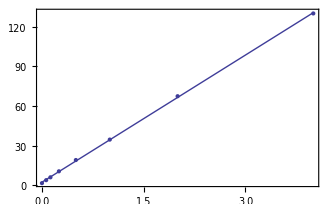

```mathematica
Block[{pp=Map[{#,First[soln[#]]}&,betaList],y},y=Fit[pp,{1,x},x];Show[ListPlot[pp,PlotRange->All,Axes->False,Frame->True],Plot[y,{x,0,4}]]]
```

```mathematica
Map[{#,soln[#][[1]],dist[soln[#][[2]]]}&,betaList]
```

{{0,1.51847,{0,0} | 623
{1,0} | 185
{1,1} | 3},{1/16,3.80224,{0,0} | 589
{0,1} | 31
{1,0} | 187
{1,1} | 4},{1/8,5.9425,{0,0} | 630
{0,1} | 30
{1,0} | 146
{1,1} | 5},{1/4,10.5006,{0,0} | 637
{0,1} | 10
{1,0} | 160
{1,1} | 4},{1/2,19.0595,{0,0} | 708
{0,1} | 65
{1,0} | 10
{1,1} | 28},{1,34.5438,{0,0} | 645
{0,1} | 7
{1,0} | 159},{2,67.4231,{0,0} | 608
{0,1} | 8
{1,0} | 195},{4,130.147,{0,0} | 637
{0,1} | 9
{1,0} | 164
{1,1} | 1}}

Compare solutions for different beta values

```mathematica
Map[{#,dist[soln[0][[2]],soln[#][[2]]]}&,betaList]
```

{{0, | {0,0} | {1,0} | {1,1}
{0,0} | 623 | 0 | 0
{1,0} | 0 | 185 | 0
{1,1} | 0 | 0 | 3},{1/16, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 586 | 30 | 7 | 0
{1,0} | 3 | 1 | 180 | 1
{1,1} | 0 | 0 | 0 | 3},{1/8, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 570 | 29 | 23 | 1
{1,0} | 60 | 1 | 123 | 1
{1,1} | 0 | 0 | 0 | 3},{1/4, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 589 | 9 | 24 | 1
{1,0} | 48 | 1 | 136 | 0
{1,1} | 0 | 0 | 0 | 3},{1/2, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 531 | 54 | 10 | 28
{1,0} | 177 | 8 | 0 | 0
{1,1} | 0 | 3 | 0 | 0},{1, | {0,0} | {0,1} | {1,0}
{0,0} | 460 | 4 | 159
{1,0} | 185 | 0 | 0
{1,1} | 0 | 3 | 0},{2, | {0,0} | {0,1} | {1,0}
{0,0} | 423 | 5 | 195
{1,0} | 185 | 0 | 0
{1,1} | 0 | 3 | 0},{4, | {0,0} | {0,1} | {1,0} | {1,1}
{0,0} | 452 | 6 | 164 | 1
{1,0} | 185 | 0 | 0 | 0
{1,1} | 0 | 3 | 0 | 0}}

### Try different methods (logistic)

Values for beta = 1.0, looks like NelderMead is fastest, although several methods find minimum.  It seems that minimum occurs for assumption that points are "far away" from the hyperplane in most methods.

```mathematica
Timing[Block[{useStep=False},soll["NelderMead"]=minP[1.0,Method->"NelderMead"]]]
```

{36.0085,{16.3563,{{-7.21134,-87.7897,-74.8709,17.5994,13.9983,12.6471,-2.64573,8.18302,-71.8016,-58.2385},{6.6533×10^18,2.15421×10^18,-1.29817×10^18,1.87021×10^18,-1.64179×10^18,-1.17187×10^18,-3.49781×10^17,1.68807×10^17,-1.02098×10^18,-3.77123×10^19}}}}

```mathematica
rewardFunction[1.0,soll["NelderMead"][[2]]]
```

25.6811

```mathematica
Timing[Block[{useStep=False},soll["DifferentialEvolution"]=minP[1.0,Method->"DifferentialEvolution"]]]
```

{124.155,{16.3563,{{-894.738,-10892.4,-9289.51,2183.62,1736.83,1569.17,-328.265,1015.3,-8908.69,-7225.87},{3.86481×10^10,1.25135×10^10,-7.54088×10^9,1.08638×10^10,-9.5369×10^9,-6.80723×10^9,-2.03183×10^9,9.80576×10^8,-5.93073×10^9,-2.19066×10^11}}}}

```mathematica
rewardFunction[1.0,soll["DifferentialEvolution"][[2]]]
```

25.6811

```mathematica
Timing[Block[{useStep=False},soll["SimulatedAnnealing"]=minP[1.0,Method->"SimulatedAnnealing"]]]
```

{37.7433,{16.3958,{{-300.413,604.133,-611.798,181.833,154.486,102.093,-21.4571,78.501,871.37,-206.964},{1.20866×10^6,391340.,-235829.,339748.,-298252.,-212885.,-63542.2,30666.,-185474.,-6.85093×10^6}}}}

```mathematica
rewardFunction[1.0,soll["SimulatedAnnealing"][[2]]]
```

26.7535

```mathematica
Timing[Block[{useStep=False},soll["RandomSearch"]=minP[1.0,Method->"RandomSearch"]]]
```

{460.248,{16.3563,{{-449171.,-5.46814×10^6,-4.66347×10^6,1.09621×10^6,871911.,787744.,-164794.,509694.,-4.47229×10^6,-3.62749×10^6},{181.921,58.9024,-35.4957,51.1371,-44.8912,-32.0424,-9.56404,4.61568,-27.9166,-1031.17}}}}

```mathematica
rewardFunction[1.0,soll["RandomSearch"][[2]]]
```

25.6811

```mathematica
Timing[Block[{useStep=False,globalMinimum=False},soll["ConjugateGradient"]=minP[1.0,Method->"ConjugateGradient"]]]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{7.41887,{16.4934,{{-0.117327,-0.724784,-0.444027,0.0582239,0.0865167,0.103864,-0.0209483,0.0653712,-0.69816,0.118356},{0.746417,4.35628,-0.644905,1.2699,-1.21268,-0.692358,-0.191049,0.157696,-1.73913,-3.62826}}}}

```mathematica
rewardFunction[1.0,soll["ConjugateGradient"][[2]]]
```

26.3575

```mathematica
Timing[Block[{useStep=False,globalMinimum=False},soll["PrincipalAxis"]=minP[1.0,Method->"PrincipalAxis"]]]
```

FindMinimum::lsbrak: Unable to bracket a minimum along the direction {0, 0.12550865415375473`, 0, 0, 0, 0, 0, 0, 0, 0} from the point {-0.06563686017330356`, -0.12550865415375473`, 0.1901308758732626`, « 4 », -0.3999405286388935`, 0.40978328093989036`, 0.39338889979834435`}.

FindMinimum::lsbrak: Unable to bracket a minimum along the direction {0, 0.0583414738710753`, 0, 0, 0, 0, 0, 0, 0, 0} from the point {0.602164570687847`, -0.0583414738710753`, 0.46632136103184874`, « 4 », -0.2600226969467423`, 0.17432140426394016`, 0.14905154772989582`}.

{42.9585,{16.3637,{{-1.13015,-17.206,-14.4187,3.38176,2.69917,2.40965,-0.509591,1.57351,-13.4752,-12.6217},{1.20229×10^13,3.8896×10^12,-2.34274×10^12,3.37744×10^12,-2.96611×10^12,-2.11753×10^12,-6.31984×10^11,3.04912×10^11,-1.84414×10^12,-6.81447×10^13}}}}

```mathematica
rewardFunction[1.0,soll["PrincipalAxis"][[2]]]
```

25.6779

```mathematica
Timing[Block[{useStep=False,globalMinimum=False},soll["Newton"]=minP[1.0,Method->"Newton"]]]
```

FindMinimum::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

{23.9064,{16.3563,{{-0.000921532,-0.0112186,-0.00956771,0.00224902,0.00178884,0.00161616,-0.000338096,0.0010457,-0.00917548,-0.00744227},{0.487405,0.157812,-0.0951008,0.137007,-0.120273,-0.0858485,-0.0256241,0.0123664,-0.0747946,-2.76272}}}}

```mathematica
rewardFunction[1.0,soll["Newton"][[2]]]
```

25.6811

```mathematica
Timing[Block[{useStep=False,globalMinimum=False},soll["QuasiNewton"]=minP[1.0,Method->"QuasiNewton"]]]
```

FindMinimum::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{4.19636,{16.5817,{{-0.16525,-2.01173,-1.71569,0.403295,0.320776,0.289811,-0.0606276,0.187516,-1.64535,-1.33455},{2.90553×10^7,1.10566×10^7,5.41676×10^7,-9.9772×10^6,-5.97041×10^6,-3.46695×10^7,-792364.,658332.,-1.28151×10^7,-2.17306×10^7}}}}

```mathematica
rewardFunction[1.0,soll["QuasiNewton"][[2]]]
```

25.0931

```mathematica
Timing[Block[{useStep=False,globalMinimum=False},soll["InteriorPoint"]=minP[1.0,Method->"InteriorPoint"]]]
```

{29.2326,{16.3958,{{-0.00146663,0.00294941,-0.00298683,0.000887716,0.00075421,0.000498422,-0.000104755,0.000383245,0.00425407,-0.00101041},{0.0141712,0.00458837,-0.00276504,0.00398347,-0.00349693,-0.00249603,-0.000745018,0.000359551,-0.00217464,-0.0803256}}}}

```mathematica
rewardFunction[1.0,soll["InteriorPoint"][[2]]]
```

26.7535

### Try different methods (step)

Values for beta = 1.0, looks like DifferentialEvolution is the winner.  Also, the local (gradient-based) methods don't do so well, as expected.

```mathematica
Timing[minP[1.0,Method->"NelderMead"]]
```

{13.8299,{27.3112,{{-1.60639,1.17417,1.69868,0.382953,1.14921,1.78659,-1.85259,-0.940264,-0.0832238,1},{0.262076,0.538741,-1.25687,0.673844,-0.45726,-0.779582,-0.864641,0.137188,0.528542,-1}}}}

```mathematica
Timing[minP[1.0,Method->"DifferentialEvolution"]]
```

{73.9947,{22.2159,{{-2.22363,-0.51215,-0.597764,-0.658475,0.373787,1.55987,-0.70285,1.79517,0.7316,1},{2.77761,1.31107,8.47791,0.812072,-1.7461,-1.07446,-3.99113,-0.257346,-2.19814,1}}}}

```mathematica
Timing[minP[1.0,Method->"SimulatedAnnealing"]]
```

{12.0962,{26.4299,{{1.08148,0.402534,-0.882877,-0.670804,-1.16722,-0.00779751,-0.370066,-0.855371,-1.26073,1},{-0.317296,-1.92537,0.562287,2.06403,0.251333,-1.41328,-1.36115,1.40593,-0.410836,1}}}}

```mathematica
Timing[minP[1.0,Method->"RandomSearch"]]
```

{74.8576,{27.4779,{{0.607712,0.916715,-0.89115,-0.645028,-0.271974,0.184948,-0.335164,-0.291924,-0.46995,-1},{0.0226535,-0.480767,0.509769,-0.625674,-0.211372,-0.524167,0.00698119,0.0724676,-0.962017,1}}}}

```mathematica
Timing[Block[{globalMinimum=False},minP[1.0,Method->"ConjugateGradient"]]]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindMinimum will be suppressed during this calculation.

{0.898864,{34.0106,{{0.287277,0.228468,-0.0829359,-0.0232021,-0.472465,-0.0260645,-0.310585,-0.204015,0.163754,-1},{-0.391736,0.110272,0.15216,-0.417394,0.44709,-0.289161,0.364883,-0.145863,0.0300254,-1}}}}

```mathematica
Timing[Block[{globalMinimum=False},minP[1.0,Method->"PrincipalAxis"]]]
```

FindMinimum::lsbrak: Unable to bracket a minimum along the direction {0, -0.24787348721335978`, 0, 0, 0, 0, 0, 0, 0} from the point {0.23817887939121962`, 0.24787348721335978`, 0.4114634145391526`, « 3 », 0.303199830579842`, -0.42421225595153067`, 0.30643595262045453`}.

{6.93295,{28.1056,{{0.240305,0.173206,0.439959,0.274375,0.172664,0.375222,-0.373519,0.408029,0.381376,-1},{-1.91306,1.10103,-0.377832,0.273106,-1.21334,0.00941127,0.135983,0.334824,-6.68727,1}}}}

```mathematica
Timing[Block[{globalMinimum=False},minP[1.0,Method->"Newton"]]]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindMinimum will be suppressed during this calculation.

{1.91971,{29.5375,{{0.141128,-0.0568138,0.356574,0.136605,0.156504,0.0454842,-0.346532,0.0189378,-0.39294,-1},{-0.112677,-0.119968,0.361145,-0.266722,-0.194544,-0.36567,-0.279983,0.290092,-0.0511178,-1}}}}

```mathematica
Timing[Block[{globalMinimum=False},minP[1.0,Method->"QuasiNewton"]]]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindMinimum will be suppressed during this calculation.

{0.85687,{37.3532,{{-0.350285,0.248926,0.346871,0.277242,0.469966,-0.255852,-0.0404521,-0.10279,-0.391178,-1},{-0.0902049,0.286367,0.368838,0.0184495,-0.160944,0.288818,0.219123,0.269524,-0.00781578,-1}}}}

```mathematica
Timing[Block[{globalMinimum=False},minP[1.0,Method->"InteriorPoint"]]]
```

{2.84157,{35.324,{{-0.488425,0.249156,0.0253755,-0.467364,0.114365,0.140335,0.0145052,0.378544,-0.148515,1},{0.399664,-0.114795,-0.0512132,0.489701,-0.478881,-0.46628,0.197257,0.195975,0.347784,-1}}}}

### Calculations for step model.

Expectation value for learning gain, 1-P(G)-P(s) in terms of: cbl = correct before learning, wbl = wrong before learning, cal = correct after learning, and wal = wrong after learning.  Not that there is a correction to the formula where we use the expectation values of P(G)=cbl/(cbl+wbl) and P(S)=wal/(cal+wal).

```mathematica
bind[x_,a_,b_]:=x^a (1-x)^b ((a+b+1)!)/(a! b!)
```

```mathematica
Integrate[bind[x,a,b],{x,0,1},Assumptions->{a>-1,b>-1}]
```

1

Note that the maximum liklihood of x, a/(a + b), is not equal to the expectation value:

```mathematica
Integrate[x bind[x,a,b],{x,0,1},Assumptions->{a>-1,b>-1}]
```

(1+a)/(2+a+b)

```mathematica
1-(pgpsbar=FullSimplify[Integrate[(g+s) bind[g,cbl ,wbl] bind[ s,wal ,cal],{g,0,1},{s,0,1},Assumptions->{cbl>-1,cal>-1,wal>-1,wbl>-1}]])
```

1-(1+wal)/(2+cal+wal)-(1+cbl)/(2+cbl+wbl)

Find the Associated variance:

```mathematica
varphps=Integrate[((g+s)-pgpsbar)^2 bind[g,cbl ,wbl] bind[ s,wal ,cal],{g,0,1},{s,0,1},Assumptions->{cbl>-1,cal>-1,wal>-1,wbl>-1}]
```

((1+cal) (1+wal))/((2+cal+wal)^2 (3+cal+wal))-(1+cbl)^2/(2+cbl+wbl)^2+((1+cbl) (2+cbl))/((2+cbl+wbl) (3+cbl+wbl))

```mathematica
First[varphps]+Simplify[Rest[varphps]]
```

((1+cal) (1+wal))/((2+cal+wal)^2 (3+cal+wal))+((1+cbl) (1+wbl))/((2+cbl+wbl)^2 (3+cbl+wbl))